SetDelayed::wrsym: Symbol Discard is Protected.

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

> Top. 1 aebe/cedf/efff.m, 0 diagrams

> Top. 2 aebe/cfde/efff.m, 0 diagrams

> Top. 3 aebe/cfdf/efef.m, 0 diagrams

> Top. 4 aebf/cede/efff.m, 0 diagrams

> Top. 5 aebf/cedf/efef.m, 0 diagrams

> Top. 6 aebf/cfde/efef.m, 0 diagrams

> Top. 7 aebf/cfdf/efee.m, 0 diagrams

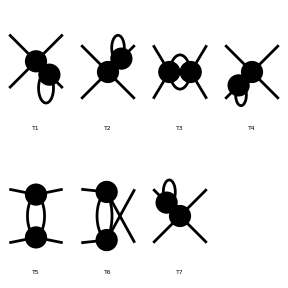

```mathematica
AppendTo[$Path,"/home/lev/Projects/mathematica/FeynArts-3.11"];
Needs["FeynArts`"];

L=1;
top=CreateTopologies[L,2->2,Adjacencies->{4},ExcludeTopologies->Tadpoles];

(*Optional preview*)
Paint[top,ColumnsXRows->4,PaintLevel->{Topologies}];
```

Topology[2][Propagator[Incoming][Vertex[1][1],Vertex[4][5]],Propagator[Incoming][Vertex[1][2],Vertex[4][5]],Propagator[Outgoing][Vertex[1][3],Vertex[4][5]],Propagator[Outgoing][Vertex[1][4],Vertex[4][6]],Propagator[Internal][Vertex[4][5],Vertex[4][6]],Propagator[Loop[1]][Vertex[4][6],Vertex[4][6]]]

> Top. 1 aebe/cedf/efff.m, 0 diagrams

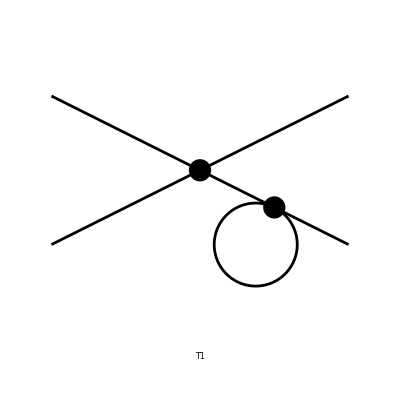

FeynArtsGraphics[2→2][([T1] | Null | Null
Null | Null | Null
Null | Null | Null)]

loading generic model file /home/lev/Projects/mathematica/FeynArts-3.11/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /home/lev/Projects/calc_mbcwc/models/Phi4MatrixSK.mod

> 1 particles (incl. antiparticles) in 1 classes

> $CounterTerms are ON

> 1 vertices

classes model {Phi4MatrixSK} initialized

inserting at level(s) {Classes}

> Top. 1: 1 Classes insertion

in total: 1 Classes insertion

TopologyList[Process→{S[1,{Col1,Col1,Con1,RAx1}],S[1,{Col2,Col2,Con2,RAx2}]}→{S[1,{Col3,Col3,Con3,RAx3}],S[1,{Col4,Col4,Con4,RAx4}]},Model→{Phi4MatrixSK},GenericModel→{Lorentz},InsertionLevel→{Classes},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{}][Topology[2][Propagator[Incoming][Vertex[1][1],Vertex[4][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[4][5],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[4][5],Field[3]],Propagator[Outgoing][Vertex[1][4],Vertex[4][6],Field[4]],Propagator[Internal][Vertex[4][5],Vertex[4][6],Field[5]],Propagator[Loop[1]][Vertex[4][6],Vertex[4][6],Field[6]]]→Insertions[Generic][FeynmanGraph[2,Generic==1][Field[1]→S[1,{Col1,Col1,Con1,RAx1}],Field[2]→S[1,{Col2,Col2,Con2,RAx2}],Field[3]→S[1,{Col3,Col3,Con3,RAx3}],Field[4]→S[1,{Col4,Col4,Con4,RAx4}],Field[5]→S,Field[6]→S]→Insertions[Classes][FeynmanGraph[2,Classes==1][Field[1]→S[1,{Col1,Col1,Con1,RAx1}],Field[2]→S[1,{Col2,Col2,Con2,RAx2}],Field[3]→S[1,{Col3,Col3,Con3,RAx3}],Field[4]→S[1,{Col4,Col4,Con4,RAx4}],Field[5]→S[1,{Col3,Col1,Con3,RAx5}],Field[6]→S[1,{Col1,Col4,Con3,RAx6}]]]]]

```mathematica
(*1) Load FeynArts and add the local model path*)
$ModelPath=Append[$ModelPath,"/home/lev/Projects/calc_mbcwc/models"];

(*2) Generate topologies:1-loop,2->2,only 4-point adjacencies,no tadpoles*)
top1 = top[[1]]
Paint[top1]
(*3) Insert fields from Phi4MatrixSK.mod with fixed OTOC external assignment*)
(*Incoming:contour 1 (r,a),Outgoing:contour 2 (r,a)*)
diags=InsertFields[top1,{S[1],S[1]}->{S[1],S[1]},Model->"Phi4MatrixSK",GenericModel->"Lorentz",InsertionLevel->{Classes}]
```